Sandri Marco (2010)
LCE package for Mathematica 7 
http://www.msandri.it
Email: sandri.marco@gmail.com

Marco Sandri (1996)
Numerical Calculation of Lyapunov Exponents
The Mathematica Journal, Volume 6, Issue 3, 79 - 84

```mathematica
SetDirectory["C:/lce_dir"];
<<lce.m
```

Estimation of LCEs of Continuous Systems - pp. 80-81
The Lorenz model

```mathematica
F[{x_,y_,z_}]:={16(y-x),x(45.92-z)-y,x y - 4z};
x0={19,20,50};
T=20;
stepsize=0.02;
n = Length[x0];
x = Array[a,n];
Phi=Array[b,{n,n}];
DPhi=Phi.Transpose[JacobianMtx[F[x],x]];
Phi0=IdentityMatrix[n];
{xT,PhiT}=IntVarEq[F[x],DPhi,x,Phi,x0,Phi0,{T,stepsize}];
xT
PhiT // MatrixForm
u =Table[Random[],{n}];
Log[Norm[PhiT.u]]/T
```

{17.733,15.0227,53.4122}

(3.19813×10^11 | -4.95999×10^12 | 5.8275×10^12
5.44679×10^11 | -8.44743×10^12 | 9.92489×10^12
2.66765×10^11 | -4.13726×10^12 | 4.86087×10^12)

1.4712

Estimation of LCEs of Continuous Systems - pp. 81-82
The Lorenz model

```mathematica
F[{x_,y_,z_}]:={16(y-x),x(45.92-z)-y,x y - 4z};
T=.1; K=800; stepsize=0.02;
x0={19,20,50};
n = Length[x0];
x = Array[a,n];
Phi=Array[b,{n,n}];
DPhi=Phi.Transpose[JacobianMtx[F[x],x]];
Phi0=IdentityMatrix[n];
s={};
xT = x0;
PhiT = Phi0;
Do[
{xT,PhiT} = IntVarEq[F[x],DPhi,x,Phi,xT,PhiT,{T,stepsize}];
W = GramSchm[PhiT];
norms=Map[Norm,W];
s = Append[s,norms];
PhiT=W/norms,
{K}];
lces=Rest[FoldList[Plus,0,Log[s]]]/(T Range[K]);
Last[lces]
```

{1.52442,-0.0162469,-22.4912}

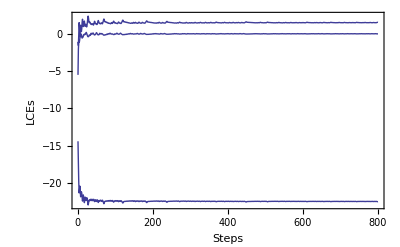

```mathematica
ConvergencePlot[lces]
```

Estimation of LCEs of Continuous Systems - pp. 81-82
The Lorenz model

{{1.50085,0.00327127,-22.4872},2.06689}

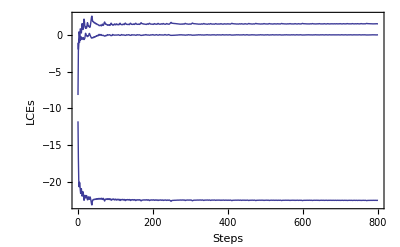

```mathematica
F[{x_,y_,z_}]:={16(y-x),x(45.92-z)-y,x y - 4z};
LCEsC[F,{19,20,50},0.1,800,20,0.02]
LCEsC[F,{19,20,50},0.1,800,20,0.02,LCEsPlot-> True]
```

Estimation of LCEs of Continuous Systems - p. 82
The Rössler model

```mathematica
rossler[{x_,y_,z_,w_}]:=
{-y-z, x+0.25 y+w, 3 + x z, 0.05 w - 0.5 z};
x0 = {-10,-14,0.3,29};
T = 0.1; K = 2000; TR=1;  stepsize=0.02;
lcesrossler = LCEsC[rossler,x0, T, K, TR,stepsize]
LyapunovDimension[First[lcesrossler]]
T = 100; TR=20;
PhaseSpaceC[rossler,x0,T,TR, stepsize,{1,2,3}]
```

{{0.142461,0.00513245,-0.0040885,-24.0835},3.00596}

3.00596

-Graphics3D-

-Graphics3D-

Estimation of LCEs of Continuous Systems - p. 82
The Duffing model

{{0.0791481,0.,-0.159148},2.49732}

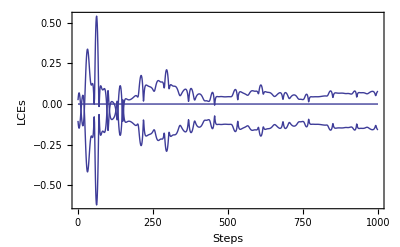

```mathematica
duffing[{x_,y_,t_}]:={y,-0.1y-x^3+10Cos[t],1}
LCEsC[duffing,{0.5,0.7,0.2},0.05,1000,10,0.02]
LCEsC[duffing,{0.5,0.7,0.2},0.05,1000,10,0.02,LCEsPlot->True]
```

LCEs of Discrete Systems
A four-dimensional discrete-time dynamical system

{{0.173841,0.158472,0.151448,-3.47949},3.13903}

3.13903

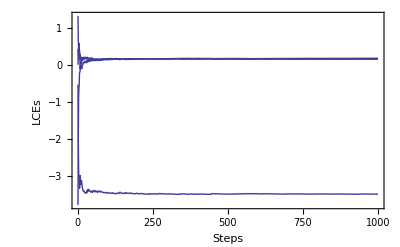

```mathematica
G[{x_,y_,z_,w_}]:={1.85-z^2 -0.05w, x, y, z}
lceshyper2 = LCEsD[G,{0.1,0,0,0}, 1000,100]
LyapunovDimension[First[lceshyper2]]
lceshyper2 = LCEsD[G,{0.1,0,0,0}, 1000,100, LCEsPlot->True]
```